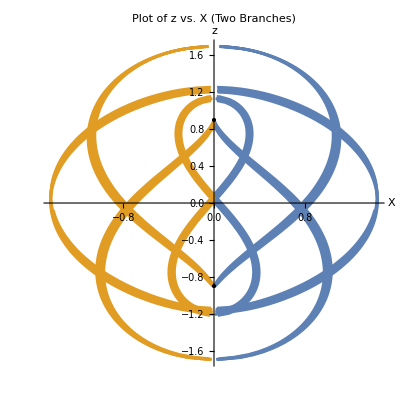

```mathematica
(*Case II parameters*)B=0;
e=0.7005;
b=0.9;

(*Relations to main parameters*)
g=Sqrt[e^2+B^2-1];

eeta[b_,e_]:=b/(1-e^2);
p=(1-e^2);

f=eeta[b,e];
ps=p[e];
d0[f_,e_]:=2/((1-f^2*(1-e^2))+Sqrt[(1-f^2*(1+e^2))^2-4*f^4*e^2]);
deltaV=f^2*d0[f,e];
eStar=e*((1+f^2*d0[f,e])/(1+f^2*d0[f,e]*e^2));
deltaR=-(((b+e)*(1-(b-e)))/((b+e)^2-(b-e)+2 Sqrt[b*e]*Sqrt[(b+e)^2-1]));
kR=((2*Sqrt[b*e]-Sqrt[(b+e)^2-1])/(2*Sqrt[b*e]+Sqrt[(b+e)^2-1]));

kS2=0.5-0.5*((1-f^2*(1-e^2))/(Sqrt[(1+f^2*(1-e^2))^2-4*f^2*B^2]));
deltaS=(-2*f*B)/(1+f^2 (1-e^2)+Sqrt[(1+f^2 (1-e^2))^2-4*f^2*B^2]);
kv=Sqrt[f^2*e^2 (1+2*f^2+f^4*(2+e^2))];
jv=Sqrt[(1-f^2 (1-e^2)+Sqrt[(1-f^2 (1-e^2))^2-4*f^2*e^2])/(1-f^2 (1-e^2)+Sqrt[(1+f^2 (1-e^2))^2-4*f^2*e^2])];
jr2=0.5*Sqrt[(2*Sqrt[b*e]+Sqrt[(b+e)^2-1])^2/(Sqrt[(1-e^2+b^2)^2-4*b^2*B^2])];

(*Case B*)
(*Define R as a function of f_v using dn and cn elliptic functions*)
(*for 0<=b<=1-e*)
R[f_,p_,deltaV_,eStar_,kv_,jv_]:=p*(JacobiDN[f*jv,kv]+deltaV*JacobiCN[f*jv,kv])/(JacobiDN[f*jv,kv]+eStar*JacobiCN[f*jv,kv]);

(*for 1-e<=b<=1+e*)
R2[f_,p_,deltaR_,b_,e_,kR_,jr2_]:=0.5*(1-b+e)*((JacobiCN[f*jr2,kR]+deltaR*JacobiDN[f*jr2,kR])/(JacobiDN[f*jr2,kR]+deltaR*JacobiCN[f*jr2,kR]))+0.5*(1+b+e);

(*Define conditional R function*)
Rconditional[f_,p_,deltaV_,eStar_,kv_,jv_,deltaR_,b_,e_,kR_,jr2_]:=Which[0<=b<=1-e,R[f,p,deltaV,eStar,kv,jv],1-e<=b<=1+e,R2[f,p,deltaR,b,e,kR,jr2]];

(*Define σ as a function of f using sn elliptic function*)
sigma[f_,fS0_,kS2_,deltaS_]:=ArcCos[((Sqrt[1-kS2^2])*JacobiSN[f+fS0,kS2]+deltaS*JacobiDN[f+fS0,kS2])/(JacobiDN[f+fS0,kS2]+(Sqrt[1-kS2^2])*deltaS*JacobiSN[f+fS0,kS2])];

(*Set parameters for σ*)
fS0=0; (*Offset for elliptic function*)

(*Define X and z in terms of R and σ,including both branches for X*)
XPlus[f_]:=Sqrt[Rconditional[f,p,deltaV,eStar,kv,jv,deltaR,b,e,kR,jr2]^2-b^2]*Sin[sigma[f,fS0,kS2,deltaS]];
XMinus[f_]:=-Sqrt[Rconditional[f,p,deltaV,eStar,kv,jv,deltaR,b,e,kR,jr2]^2-b^2]*Sin[sigma[f,fS0,kS2,deltaS]];
z[f_]:=Rconditional[f,p,deltaV,eStar,kv,jv,deltaR,b,e,kR,jr2]*Cos[sigma[f,fS0,kS2,deltaS]];

(*Define specific points to be included*)
specificPoints={{0,b},{0,-b}};

(*Plot z vs.X for both branches of X as a parametric plot by varying f*)
Show[ParametricPlot[{{XPlus[f],z[f]},{XMinus[f],z[f]}},{f,0,25Pi},PlotRange->All,PlotLabel->"Plot of z vs. X (Two Branches)",AxesLabel->{"X","z"},AspectRatio->1,PlotStyle->{LightOrangeOrange,LightBlueBlue}],ListPlot[specificPoints,PlotStyle->{Black,PointSize[Large]}]]
```